```mathematica
tuples=Tuples[{0,1},{3,3}];
n=Length[tuples];
side=Ceiling[Sqrt[n]];
padded=PadRight[tuples,{side^2,3,3}];
blocks=Partition[padded,side];
bigMatrix=ArrayFlatten[blocks];
centers=Flatten[Table[{i,j},{i,Range[2,69,3]},{j,Range[2,69,3]}],1];
ArrayPlot[bigMatrix,Mesh->{Range[0,27*3,3],Range[0,27*3,3]},MeshStyle->Directive[Gray,Thick]]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
fns=FileNames["t_*.mat","./"];
data=Import[#,"MAT"]&/@fns;
datos=AssociationMap[Import[#,"MAT"]&,fns];
```

```mathematica
base=Import["../../CA/B3S238/base.mat","MAT"];
```

```mathematica
base[[1,2]]==#&/@datos[[;;,1,2]]
```

<|./t_00001.mat→True,./t_00002.mat→True,./t_00003.mat→True,./t_00004.mat→True,./t_00005.mat→True,./t_00006.mat→True,./t_00007.mat→True,./t_00008.mat→True,./t_00009.mat→True,./t_0001.mat→True,./t_0002.mat→True,./t_0003.mat→True,./t_0004.mat→True,./t_0005.mat→True,./t_0006.mat→True,./t_0007.mat→True,./t_0008.mat→True,./t_0009.mat→True,./t_001.mat→True,./t_002.mat→True,./t_003.mat→False,./t_004.mat→False,./t_005.mat→False,./t_006.mat→False,./t_007.mat→False,./t_008.mat→False,./t_009.mat→False,./t_01.mat→False,./t_02.mat→True,./t_03.mat→False|>

```mathematica
basevector=Flatten[Part[base[[1,2]],#[[1]],#[[2]]]&/@{#}&/@centers];
```

```mathematica
vectors=Table[
Flatten[Part[i,#[[1]],#[[2]]]&/@{#}&/@centers],
{i,datos[[;;,1,2]]}
];
```

```mathematica
names=ToExpression["0."<>StringJoin[Characters[#][[6;;-5]]]]&/@Keys[datos];
```

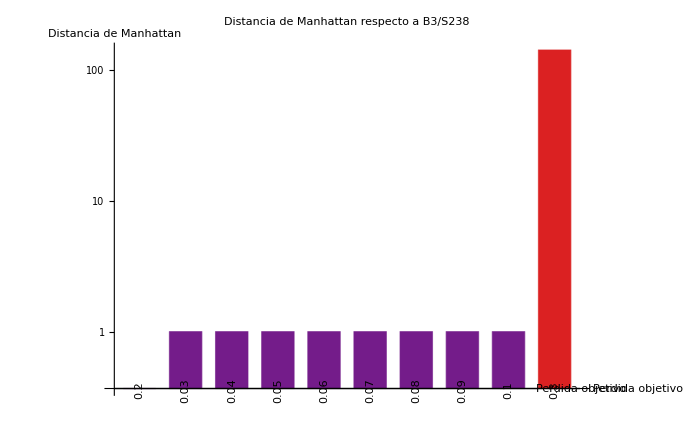

```mathematica
distancias=ManhattanDistance[basevector,#]&/@vectors;
orden=Reverse@Ordering[distancias,All,Greater];
namesSorted=names[[orden]];
distSorted=distancias[[orden]];

primerNoCero=FirstPosition[distSorted,x_/;x>0][[1]];
mask=Table[distSorted[[i]]>0||i==primerNoCero-1,{i,Length[distSorted]}];

namesFiltered=Pick[namesSorted,mask];
distFiltered=Pick[distSorted,mask];

(*Colorear según el VALOR,no según la posición*)
colorFunc=ColorData["Rainbow"];
valoresEscalados=Rescale[distFiltered]; (*normaliza entre 0 y 1*)
coloresPorValor=colorFunc/@valoresEscalados;

fplot=BarChart[distFiltered,ChartStyle->coloresPorValor,ChartLabels->Placed[Rotate[#,90 Degree]&/@namesFiltered,Axis],ScalingFunctions->"Log",AxesLabel->{"Perdida objetivo","Distancia de Manhattan"},PlotLabel->"Distancia de Manhattan respecto a B3/S238",ImageSize->700,LabelStyle->Directive[FontSize->11],BarSpacing->0.42]
```

```mathematica
life=Import["../../CA/B3S23/base.mat","MAT"];
lifevector=Flatten[Part[life[[1,2]],#[[1]],#[[2]]]&/@{#}&/@centers];
```

```mathematica
datos["./t_01.mat"][[1,2]]==life[[1,2]]
```

True

```mathematica
Keys[datos]
```

{./t_00001.mat,./t_00002.mat,./t_00003.mat,./t_00004.mat,./t_00005.mat,./t_00006.mat,./t_00007.mat,./t_00008.mat,./t_00009.mat,./t_0001.mat,./t_0002.mat,./t_0003.mat,./t_0004.mat,./t_0005.mat,./t_0006.mat,./t_0007.mat,./t_0008.mat,./t_0009.mat,./t_001.mat,./t_002.mat,./t_003.mat,./t_004.mat,./t_005.mat,./t_006.mat,./t_007.mat,./t_008.mat,./t_009.mat,./t_01.mat,./t_02.mat,./t_03.mat}

```mathematica
ArrayPlot[vectors,Mesh->True]
```

-Graphics-

```mathematica
ArrayPlot[{basevector[[-100;;-50]],vectors[[-3,-100;;-50]],lifevector[[-100;;-50]]},FrameTicks->{{{{1,"vectors[[-3]]"},{2,"lifevector"}},None},(*{left,right}*){None,None}                                         (*{bottom,top}*)},Mesh->True]
```

-Graphics-

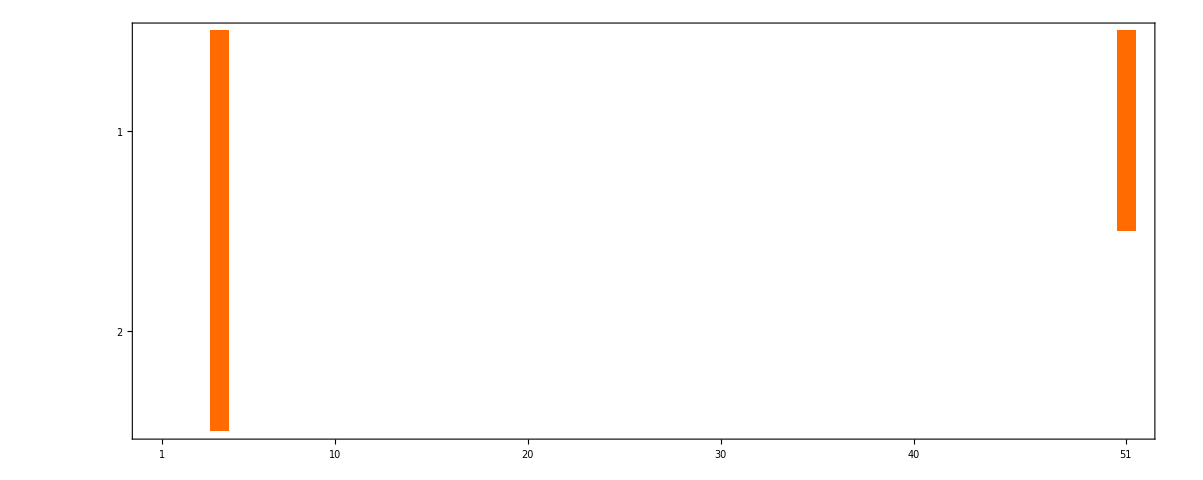

```mathematica
MatrixPlot[
{
basevector[[-68;;-18]],
lifevector[[-68;;-18]]
},Mesh->Automatic
]
```

```mathematica
Keys[datos][[-11]]
```

./t_002.mat

```mathematica
fplotc=MatrixPlot[{
basevector[[-68;;-18]],
lifevector[[-68;;-18]],
vectors[[-2,-68;;-18]],
vectors[[-3,-68;;-18]],
vectors[[-4,-68;;-18]],
vectors[[-5,-68;;-18]],
vectors[[-6,-68;;-18]],
vectors[[-7,-68;;-18]],
vectors[[-8,-68;;-18]],
vectors[[-9,-68;;-18]],
vectors[[-10,-68;;-18]],
vectors[[-11,-68;;-18]]
},FrameTicks->{{{{1,"B3/S238"},{2,"B3/S23"},{3,"NCA(0.2)"},{4,"NCA(0.1)"},{5,"NCA(0.09)"},{6,"NCA(0.08)"},{7,"NCA(0.07)"},{8,"NCA(0.06)"},{9,"NCA(0.05)"},{10,"NCA(0.04)"},{11,"NCA(0.03)"},{12,"NCA(0.02)"}},None},{None,None}},PlotLabel->"Comparación de vectores",ImagePadding->{{100,10},{30,30}},ImageSize->500,Mesh->True];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["../../../../Documentation/img/b3s238_vector.png",fplotc];
```